```mathematica
Get["https://raw.githubusercontent.com/szhorvat/IGraphM/master/IGInstaller.m"]
```

The currently installed versions of IGraph/M are: {}

Installing IGraph/M is complete: PacletObject[…].

It can now be loaded using the command <<IGraphM`

```mathematica
<<IGraphM`;
rasterTrick[plot_]:=Show[plot,Prolog->{Opacity[0],Texture[{{{0,0,0,0}}}],VertexTextureCoordinates->{{0,0},{1,0},{1,1}},Polygon[{{0,0},{.1,0},{.1,.1}}]}]
(*https://mathematica.stackexchange.com/questions/18625/avoiding-grid-lines-inside-filled-area-in-regionplot-exported-as-pdf*)
```

```mathematica
db = DatabaseReference[FindFile[NotebookDirectory[]<>"/../data/genova.db"]]
```

DatabaseReference[…]

```mathematica
queryGraphLinks = ExternalEvaluate[db, "
	WITH e(edge_id, node_from_id, node_to_id) AS (
		SELECT geo_edges.edge_id, geo_edges.node_from_id, geo_edges.node_to_id
		FROM geo_edges
		
	), g(edge_id, node_from_id, node_to_id) AS (
		SELECT geo_edges.edge_id, geo_edges.node_from_id, geo_edges.node_to_id
		FROM geo_edges
		
	)
	SELECT ABS(g.edge_id) as \"from\", ABS(e.edge_id) AS \"to\"
	FROM e
	INNER JOIN g
	WHERE e.node_to_id = g.node_from_id AND ABS(g.edge_id) <> ABS(e.edge_id)
	UNION
	SELECT ABS(e.edge_id) AS \"from\", ABS(g.edge_id) as \"to\"
	FROM e
	INNER JOIN geo_edges g
	WHERE e.node_from_id = g.node_to_id AND ABS(g.edge_id) <> ABS(e.edge_id)
;"];

(* We select the absolute, treat F and T roads as the same. This simplifies graph and reduces computation time. Since data is bad anyways, I don't think this will affect the results by much.*)
```

```mathematica
(* We select max because we are interested on the study of the congested direction of the road*)
queryTrafficData = ExternalEvaluate[db, "
	SELECT
		g.edge_id AS edge_id,
		MAX(t.count_mean) AS count
	FROM geo_edges g
	INNER JOIN traffic_data t
	ON g.edge_id = ABS(t.edge_id)
	WHERE t.hour_slot = 170
	GROUP BY g.edge_id
;"];
```

```mathematica
graphLinks = Thread[#["from"]<-> #["to"] /. #]&/@Normal[queryGraphLinks];
g=Graph[graphLinks,VertexLabels->None];
validNodes = queryTrafficData[[;;, 1]];
invalidNodes = Select[VertexList[g], !MemberQ[validNodes, #]&];
g = VertexDelete[g, invalidNodes];
disconnectedNodes = Flatten[ConnectedComponents[g][[2;;]]]; (* Remove disconnected train network *)
g = VertexDelete[g, disconnectedNodes];
```

```mathematica
Rasterize[GraphPlot[g], RasterSize->1000]
```

-Graphics-

```mathematica
Count[VertexDegree[g], 2] (* Are there relatively few nodes with only two degrees? Can we go on without simplifying the graph? *)
```

530

```mathematica
queryTrafficData
```

Dataset[<>]

```mathematica
ToAssociations = ResourceFunction["ToAssociations"];
neighborsOf = ToAssociations[# ->VertexList@VertexDelete[NeighborhoodGraph[g, #], #] &/@ VertexList[g]];
carCount =ToAssociations[ #["edge_id"]->#["count"]&/@ Normal[queryTrafficData]];
```

```mathematica
neighborsOf[55262035]
carCount[55262035]
```

{55262034,55262068}

0.193548

```mathematica
GetSpeedAndDensityOfSingleRoad = (edgeId) ↦ Module[{queryNodeCapacity, speedValues, densityValues},
queryNodeCapacity = ExternalEvaluate[db, "
		SELECT
			t.hour_slot as time, MAX(t.count_mean / g.edge_length) AS density, MIN(t.speed_mean)*MAX(t.count_mean / g.edge_length) AS flux
		FROM traffic_data t
		INNER JOIN geo_edges g
		ON g.edge_id = t.edge_id AND ABS(t.edge_id) = "<>ToString[edgeId]<>"
		GROUP BY t.hour_slot
	;"];
fluxValues = Normal@Transpose[queryNodeCapacity]["flux"];
densityValues = Normal@Transpose[queryNodeCapacity]["density"];

{densityValues, fluxValues} // Transpose
];

PlotCongestionOfSingleRoad = (edgeId) ↦ Module[{},
ListPlot[GetSpeedAndDensityOfSingleRoad[edgeId], PlotRange->All]
];
```

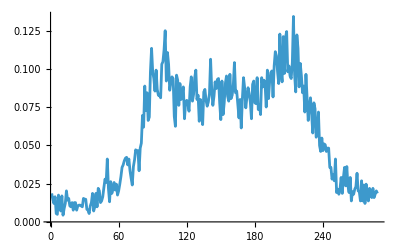

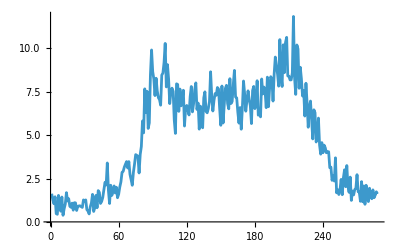

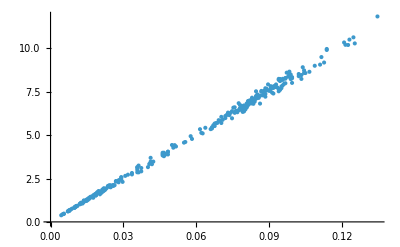

```mathematica
testRoad = GetSpeedAndDensityOfSingleRoad[55255453];
ListLinePlot[testRoad[[;;, 1]]]
ListLinePlot[testRoad[[;;, 2]]]
ListPlot[testRoad]
```

```mathematica
validNodes = VertexList[g];
$DefaultParallelKernels= {7};
LaunchKernels[];
heatmapPoints = ParallelMap[GetSpeedAndDensityOfSingleRoad, validNodes[[2150;;2250]], Method->"ItemsPerEvaluation" -> 10];
```

LaunchKernels::nodef: Some parallel subkernels are already running. Not launching default kernels again.

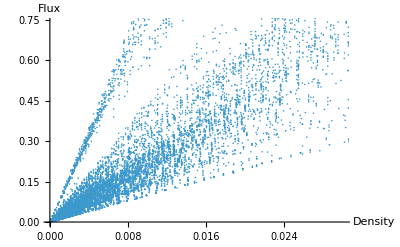

```mathematica
ListPlot[Flatten[heatmapPoints, 1], AxesLabel->{"Density", "Flux"}]
```

```mathematica
queryNodeCapacity = ExternalEvaluate[db, "
		SELECT
			t.hour_slot as time, MAX(t.count_mean / g.edge_length) AS density, MIN(t.speed_mean) AS speed
		FROM traffic_data t
		INNER JOIN geo_edges g
		ON g.edge_id = t.edge_id AND ABS(t.edge_id) = "<>ToString[edgeId]<>"
		GROUP BY t.hour_slot
	;"];
GPUArray@queryNodeCapacity
```

GPUArray::nogpu: No supported GPUs were detected on the system.

GPUArray[Failure[…]]